```mathematica
SumCot[n_] := -(-1)^n 2^(2 n)BernoulliB[2 n]/(2 n)! Phi[2 n,N];
```

```mathematica
AsymSumCot[n_] := 2^(2 n)2(2n)!Zeta[2 n]/(2 n+1)! /(2 Pi)^(2 n)N^(2 n +1)/Zeta[2 n +1];
```

```mathematica
2^(2 n)2(2n)!Zeta[2 n]/(2 n+1)! /(2 Pi)^(2 n)N^(2 n +1)/Zeta[2 n +1]//FullSimplify
```

(2 N^(1+2 n) π^(-2 n) Zeta[2 n])/((1+2 n) Zeta[1+2 n])

```mathematica
Fall[0]
```

0

```mathematica
Pall[x_]:=Sum[EulerPhi[k]Residue[(2 π^(-2 n))/(1+2 n) x^(-n +1) k^(-2 n -1),{n , -1/2}],{k ,1,Floor[1/(Pi Sqrt[x])]}]
```

```mathematica
Pall[x]
```

∑_(k=1)^Floor[1/(π √x)] π x^(3/2) EulerPhi[k]

```mathematica
2/5 Pi^(-4)Zeta[4]/Zeta[5]
```

1/(225 Zeta[5])

```mathematica
N[1/(225 Zeta[5])]
```

0.00428617

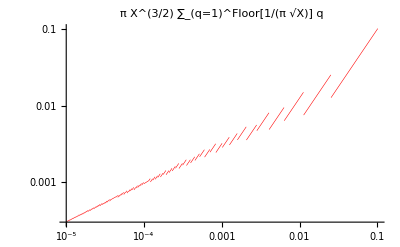

```mathematica
S1 =LogLogPlot[Pi z Sqrt[z]Sum[EulerPhi[k],{k ,1,Floor[1/(Pi Sqrt[z])]}],{z,10^(-5),1/Pi^2},PlotLabel->X Sqrt[X]Pi Phi[Floor[1/(Pi Sqrt[X])]], PlotStyle->{Red,  Thickness[0.001]}]//Quiet
```